# Interpolation Error: Estimation

Harri Hakula, 2021

## Setup

We use the same set of  nodes x_i for interpolating two functions below.

```mathematica
xp = Subdivide[0,1,3]
```

{0,1/3,2/3,1}

## Case 1: f(x) = e^x

```mathematica
f[x_]:=Exp[x];
```

```mathematica
yp=f[xp];
```

```mathematica
data=Transpose[{xp,yp}];
```

```mathematica
ip=InterpolatingPolynomial[data,x];
```

```mathematica
n=Exponent[ip,x]
```

3

Let us plot the absolute value of the error.

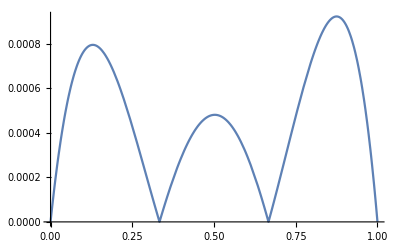

```mathematica
Plot[Abs[f[x]-ip],{x,0,1}]
```

Over the interval, the absolute value of the 4th derivative of the function is bounded from above by M = e:

```mathematica
M=Exp[1];
```

We need to maximize the absolute value of the product term. We proceed as usual, here we can cheat and use the power of Mathematica.

```mathematica
pr=Times@@(x-xp);
```

```mathematica
max=First@Maximize[{pr,0≤x≤1},x]
min=First@Minimize[{pr,0≤x≤1},x]
```

1/144

1/54 (3-√5) (-1+1/6 (3-√5)) (-2+1/2 (3-√5)) (-1+1/2 (3-√5))

```mathematica
bound=Max[Abs[min],Abs[max]]
```

1/54 (3-√5) (1+1/6 (-3+√5)) (1+1/2 (-3+√5)) (2+1/2 (-3+√5))

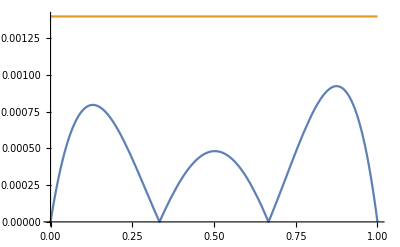

```mathematica
Plot[{Abs[f[x]-ip],M bound/(n+1)!},{x,0,1}]
```

Of course, we could skip the estimation and compute directly.

```mathematica
max=First@NMaximize[{Abs[f[x]-ip],0≤x≤1},x]
```

0.00092402

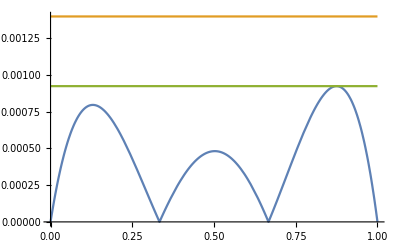

```mathematica
Plot[{Abs[f[x]-ip],M bound/(n+1)!,max},{x,0,1}]
```

## Case 2: f(x) = sin(x)

```mathematica
f[x_]:=Sin[x];
```

```mathematica
yp=f[xp];
```

```mathematica
data=Transpose[{xp,yp}];
```

```mathematica
ip=InterpolatingPolynomial[data,x];
```

```mathematica
n=Exponent[ip,x]
```

3

Let us plot the absolute value of the error.

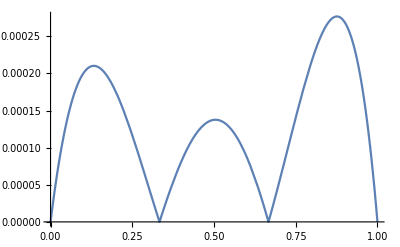

```mathematica
Plot[Abs[f[x]-ip],{x,0,1}]
```

Over the interval, the absolute value of the 4th derivative of the function is bounded from above by M = 1:

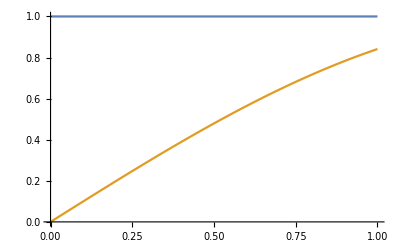

```mathematica
Plot[{1,Sin[x]},{x,0,1}]
```

```mathematica
M=1;
```

We need to maximize the absolute value of the product term. We proceed as usual, here we can cheat and use the power of Mathematica.

```mathematica
pr=Times@@(x-xp);
```

```mathematica
max=First@Maximize[{pr,0≤x≤1},x]
min=First@Minimize[{pr,0≤x≤1},x]
```

1/144

1/54 (3-√5) (-1+1/6 (3-√5)) (-2+1/2 (3-√5)) (-1+1/2 (3-√5))

```mathematica
bound=Max[Abs[min],Abs[max]]
```

1/54 (3-√5) (1+1/6 (-3+√5)) (1+1/2 (-3+√5)) (2+1/2 (-3+√5))

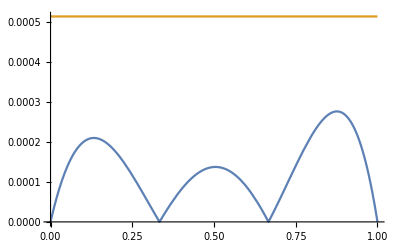

```mathematica
Plot[{Abs[f[x]-ip],M bound/(n+1)!},{x,0,1}]
```

Of course, we could skip the estimation and compute directly.

```mathematica
max=First@NMaximize[{Abs[f[x]-ip],0≤x≤1},x]
```

0.000276663

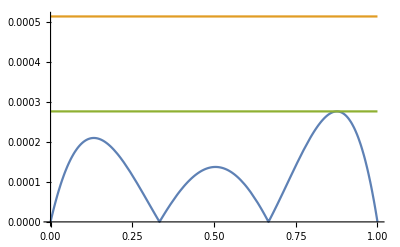

```mathematica
Plot[{Abs[f[x]-ip],M bound/(n+1)!,max},{x,0,1}]
```

Amusingly, 1/3456 is a pretty good approximation.

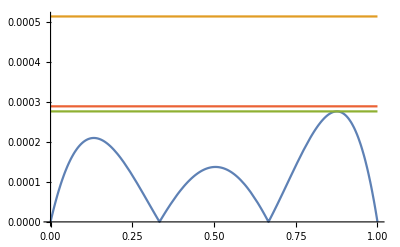

```mathematica
Plot[{Abs[f[x]-ip],M bound/(n+1)!,max,1/3456},{x,0,1}]
```